```mathematica
sol=NDSolve[{D[u[x],{x,2}]+u[x]^3==Sin[x],u[0]==0,u[1]==1},u,{x,0,1}]
```

```mathematica
{{u->InterpolatingFunction[…]}}
```

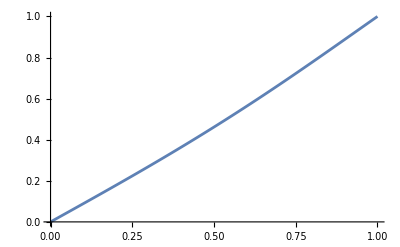

```mathematica
Plot[Evaluate[u[x]/.sol], {x, 0, 1}, AxesOrigin->{0,0}]
```

```mathematica
Grid[Table[{x,u[x]/.sol/.{val_}:>val},{x,0,1,N[1/99]}]]
```

0. | 0.
0.010101 | 0.00893445
0.020202 | 0.0178699
0.030303 | 0.0268074
0.040404 | 0.0357481
0.0505051 | 0.0446928
0.0606061 | 0.0536427
0.0707071 | 0.0625987
0.0808081 | 0.0715619
0.0909091 | 0.0805334
0.10101 | 0.089514
0.111111 | 0.0985048
0.121212 | 0.107507
0.131313 | 0.116521
0.141414 | 0.125549
0.151515 | 0.13459
0.161616 | 0.143647
0.171717 | 0.15272
0.181818 | 0.16181
0.191919 | 0.170918
0.20202 | 0.180045
0.212121 | 0.189192
0.222222 | 0.198359
0.232323 | 0.207549
0.242424 | 0.216761
0.252525 | 0.225996
0.262626 | 0.235256
0.272727 | 0.24454
0.282828 | 0.253851
0.292929 | 0.263189
0.30303 | 0.272554
0.313131 | 0.281948
0.323232 | 0.29137
0.333333 | 0.300823
0.343434 | 0.310306
0.353535 | 0.319821
0.363636 | 0.329367
0.373737 | 0.338946
0.383838 | 0.348559
0.393939 | 0.358205
0.40404 | 0.367886
0.414141 | 0.377601
0.424242 | 0.387353
0.434343 | 0.39714
0.444444 | 0.406964
0.454545 | 0.416825
0.464646 | 0.426724
0.474747 | 0.43666
0.484848 | 0.446634
0.494949 | 0.456647
0.505051 | 0.466698
0.515152 | 0.476789
0.525253 | 0.486919
0.535354 | 0.497088
0.545455 | 0.507296
0.555556 | 0.517544
0.565657 | 0.527832
0.575758 | 0.53816
0.585859 | 0.548527
0.59596 | 0.558934
0.606061 | 0.56938
0.616162 | 0.579866
0.626263 | 0.59039
0.636364 | 0.600953
0.646465 | 0.611555
0.656566 | 0.622195
0.666667 | 0.632873
0.676768 | 0.643588
0.686869 | 0.654339
0.69697 | 0.665127
0.707071 | 0.67595
0.717172 | 0.686808
0.727273 | 0.6977
0.737374 | 0.708625
0.747475 | 0.719583
0.757576 | 0.730571
0.767677 | 0.74159
0.777778 | 0.752639
0.787879 | 0.763715
0.79798 | 0.774818
0.808081 | 0.785947
0.818182 | 0.7971
0.828283 | 0.808276
0.838384 | 0.819473
0.848485 | 0.83069
0.858586 | 0.841925
0.868687 | 0.853176
0.878788 | 0.864442
0.888889 | 0.87572
0.89899 | 0.88701
0.909091 | 0.898307
0.919192 | 0.909612
0.929293 | 0.92092
0.939394 | 0.932231
0.949495 | 0.943541
0.959596 | 0.954849
0.969697 | 0.966151
0.979798 | 0.977446
0.989899 | 0.988729
1. | 1.

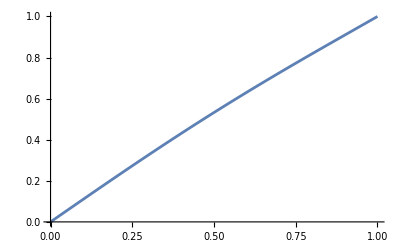

```mathematica
data = {{0,0},{0.010101,0.0111316},{0.020202,0.0222623},{0.030303,0.0333908},{0.040404,0.0445163},{0.0505051,0.0556377},{0.0606061,0.0667539},{0.0707071,0.077864},{0.0808081,0.0889669},{0.0909091,0.100062},{0.10101,0.111147},{0.111111,0.122223},{0.121212,0.133287},{0.131313,0.144339},{0.141414,0.155378},{0.151515,0.166404},{0.161616,0.177414},{0.171717,0.188408},{0.181818,0.199386},{0.191919,0.210346},{0.20202,0.221287},{0.212121,0.232209},{0.222222,0.243111},{0.232323,0.253992},{0.242424,0.264851},{0.252525,0.275688},{0.262626,0.286501},{0.272727,0.29729},{0.282828,0.308054},{0.292929,0.318793},{0.30303,0.329505},{0.313131,0.340191},{0.323232,0.350849},{0.333333,0.361479},{0.343434,0.372081},{0.353535,0.382654},{0.363636,0.393197},{0.373737,0.40371},{0.383838,0.414192},{0.393939,0.424643},{0.40404,0.435063},{0.414141,0.445452},{0.424242,0.455808},{0.434343,0.466132},{0.444444,0.476423},{0.454545,0.486681},{0.464646,0.496907},{0.474747,0.507099},{0.484848,0.517258},{0.494949,0.527383},{0.505051,0.537475},{0.515152,0.547533},{0.525253,0.557558},{0.535354,0.567549},{0.545455,0.577506},{0.555556,0.587431},{0.565657,0.597322},{0.575758,0.60718},{0.585859,0.617006},{0.59596,0.626799},{0.606061,0.63656},{0.616162,0.646289},{0.626263,0.655986},{0.636364,0.665653},{0.646465,0.675289},{0.656566,0.684894},{0.666667,0.694471},{0.676768,0.704018},{0.686869,0.713537},{0.69697,0.723028},{0.707071,0.732493},{0.717172,0.741931},{0.727273,0.751343},{0.737374,0.760731},{0.747475,0.770095},{0.757576,0.779437},{0.767677,0.788756},{0.777778,0.798055},{0.787879,0.807334},{0.79798,0.816594},{0.808081,0.825837},{0.818182,0.835064},{0.828283,0.844275},{0.838384,0.853472},{0.848485,0.862657},{0.858586,0.871831},{0.868687,0.880995},{0.878788,0.890151},{0.888889,0.899301},{0.89899,0.908445},{0.909091,0.917586},{0.919192,0.926725},{0.929293,0.935864},{0.939394,0.945006},{0.949495,0.95415},{0.959596,0.963301},{0.969697,0.972459},{0.979798,0.981627},{0.989899,0.990806},{1,1}};
ListPlot[data, Joined->True]
```